```mathematica
(* MA39110 / Assignment 4.3 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
BlockThomas[a_, b_, c_, d_]:=Module[{b1=Array[0&,{Length[b],1,2,2}],c1=Array[0&,{Length[c],1,2,2}],d1=Array[0&,{Length[d],1,2,1}],x=Array[0&,{Length[b],1,2,1}]},
c1[[1,1]]=Dot[Inverse[b[[1,1]]],c[[1,1]]]; d1[[1,1]]=Dot[Inverse[b[[1,1]]],d[[1,1]]];
Do[
b1[[i,1]]=b[[i,1]]-Dot[a[[i-1,1]],c1[[i-1,1]]];
If[i≠Length[d],c1[[i,1]]=Dot[Inverse[b1[[i,1]]],c[[i,1]]];];
d1[[i,1]]=Dot[Inverse[b1[[i,1]]],d[[i,1]]-Dot[a[[i-1,1]],d1[[i-1,1]]]];
,{i,2,Length[d]}];
x[[Length[b],1]]=d1[[Length[b],1]];
Do[
x[[i,1]]=d1[[i,1]]-Dot[c1[[i,1]],x[[i+1,1]]];
,{i,Length[b]-1,1,-1}];
x];
Model[n0_]:=Module[{n=n0},
x0=0;xf=10;h=(xf-x0)/n;
a=Array[{{0,0},{0,0}}&,{n-2,1}];
b=Array[{{0,0},{0,0}}&,{n-1,1}];
c=Array[{{0,0},{0,0}}&,{n-2,1}];
d=Array[{0,0}&,{n-1,1}];
eps=0.01;
X=Table[x0+x*h,{x,1,n-1}];
XT=Table[x0+x*h,{x,0,n}];
(* Initial Approximation: f(x)=(19x^3-317x^2+1288x)/648 *)
fT=N[(19XT^3-317XT^2+1288XT)/648];
FT=Flatten[{{0},N[(57X^2-634X+1288)/648],{1}}];
While[{
f=fT;F=FT;
For[i=1,i<n,i++,
{
im=i+1;
b[[i,1]]={{1,-h/2},{(F[[im+1]]-F[[im-1]])/(2h),-2/h^2-2F[[im]]}};
d[[i,1]]={-f[[im]]+f[[im-1]]+(h/2)(F[[im]]+F[[im-1]]),-(1/h^2)(F[[im-1]]-2F[[im]]+F[[im+1]])-(1/(2h))f[[im]](F[[im+1]]-F[[im-1]])+F[[im]]^2-1};
If[i≠n-1,{a[[i,1]]={{-1,-h/2},{0,1/h^2-f[[im+1]]/(2h)}},c[[i,1]]={{0,0},{0,1/h^2+f[[im]]/(2h)}}}];
}];
FT=F+Flatten[{{0},Flatten[BlockThomas[a,b,c,d]][[2;;;;2]],{0}}];
fT=f+Flatten[{{0},Flatten[BlockThomas[a,b,c,d]][[1;;;;2]],{0}}];};N[Max[Abs[fT-f]]]>eps];
XT=XT[[1;;-2;;1]];
fT=fT[[1;;-2;;1]];
fT];
```

```mathematica
in={20,40, 80};
sol=Model[in[[1]]];
solt=NDSolve[{y'''[x]+y[x]y''[x]+1-y'[x]^2==0,y[0]==y'[0]==0,y'[10]==1},y[x],x];
err1=Abs[NDSolveValue[{y'''[x]+y[x]y''[x]+1-y'[x]^2==0,y[0]==y'[0]==0,y'[10]==1},y[XT],x]-sol];
perr1=ListPlot[Transpose[{XT,err1}],PlotStyle->Red];
Print[N[Max[err1]]];
p1=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18]]},{ListPlot[Transpose[{XT,sol}],PlotStyle->Red]},{Plot[(19x^3-317x^2+1288x)/648,{x,0,10},PlotStyle->{Dashed,Black}]}];
```

0.0534011

```mathematica
sol=Model[in[[2]]];
solt=NDSolve[{y'''[x]+y[x]y''[x]+1-y'[x]^2==0,y[0]==y'[0]==0,y'[10]==1},y[x],x];
err2=Abs[NDSolveValue[{y'''[x]+y[x]y''[x]+1-y'[x]^2==0,y[0]==y'[0]==0,y'[10]==1},y[XT],x]-sol];
perr2=ListPlot[Transpose[{XT,err2}],PlotStyle->Green];
Print[N[Max[err2]]];
p2=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18]]},{ListPlot[Transpose[{XT,sol}],PlotStyle->Red]},{Plot[(19x^3-317x^2+1288x)/648,{x,0,10},PlotStyle->{Dashed,Black}]}];
```

0.0163164

```mathematica
sol=Model[in[[3]]];
solt=NDSolve[{y'''[x]+y[x]y''[x]+1-y'[x]^2==0,y[0]==y'[0]==0,y'[10]==1},y[x],x];
err3=Abs[NDSolveValue[{y'''[x]+y[x]y''[x]+1-y'[x]^2==0,y[0]==y'[0]==0,y'[10]==1},y[XT],x]-sol];
perr3=ListPlot[Transpose[{XT,err3}],PlotStyle->Blue];
Print[N[Max[err3]]];
p3=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style[StringForm["h = ``",N[h]],FontSize->18]]},{ListPlot[Transpose[{XT,sol}],PlotStyle->Red]},{Plot[(19x^3-317x^2+1288x)/648,{x,0,10},PlotStyle->{Dashed,Black}]}];
```

0.00470185

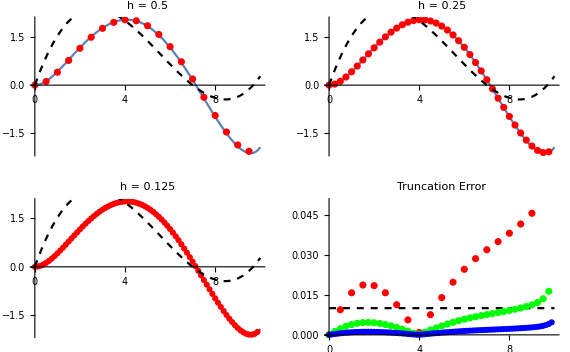

```mathematica
p4=Show[{Plot[y[x]=10^-2,{x,0,10},PlotStyle->{Dashed,Black}]},{perr1},{perr2},{perr3},PlotLabel->Style["Truncation Error",FontSize->18],PlotRange->{{0,10},{0,0.05}}];
GraphicsGrid[{{p1,p2},{p3,p4}}]
```